# Exact Multivariate Amplitude Distributions

## Implementation Test

## Juan Camilo Henao Londono

## Gaussian-Gaussian Probability Density Function

```mathematica
PDFGaussianGaussian[Returns_, N_, Λ_] := 1/(2^((N-1)/2) Gamma[N/2] √((π Λ)/N))(√((N Returns^2)/Λ))^((N-1)/2)BesselK[(1-N)/2,√((N Returns^2)/Λ)]
```

```mathematica
PDFGaussianGaussian::usage="Computes the one dimensional Gaussian-Gaussian probability density function with parameters N and Λ."
```

Computes the one dimensional Gaussian-Gaussian probability density function with parameters N and Λ.

```mathematica
NIntegrate[PDFGaussianGaussian[R, 5, 1], {R, -Infinity, +Infinity}]
```

1.

```mathematica
PDFGG = N[Table[PDFGaussianGaussian[r, 5,1], {r,-10,10}]]
```

Infinity::indet: Indeterminate expression (0 √5 ComplexInfinity)/(3 π) encountered.

{6.6374×10^-9,5.34976×10^-8,4.24147×10^-7,3.29434×10^-6,0.0000249204,0.000182007,0.00126568,0.00817967,0.0468178,0.210705,Indeterminate,0.210705,0.0468178,0.00817967,0.00126568,0.000182007,0.0000249204,3.29434×10^-6,4.24147×10^-7,5.34976×10^-8,6.6374×10^-9}

## Gaussian-Algebraic Probability Density Function

```mathematica
PDFGaussianAlgebraic[Returns_, K_, L_, N_, Λ_] := (Gamma[L-(K+N)/2+1]Gamma[L-(K-1)/2])/(Gamma[L-(K+N-1)/2]Gamma[N/2] √(2π Λ(2L-K-N-1)/N))HypergeometricU[L-(K+N)/2+1,(1-N)/2+1,(N Returns^2)/(2(2L-K-N-1)Λ)]
```

```mathematica
NIntegrate[PDFGaussianAlgebraic[R, 100, 55, 5, 1], {R, -Infinity, +Infinity}]
```

1.

```mathematica
PDFGA=N[Table[PDFGaussianAlgebraic[r,100,55,5,1], {r,-10,10}]]
```

{0.0000113559,0.0000223223,0.0000468394,0.000106208,0.000264233,0.00073491,0.00233595,0.00867787,0.0380445,0.184918,0.557539,0.184918,0.0380445,0.00867787,0.00233595,0.00073491,0.000264233,0.000106208,0.0000468394,0.0000223223,0.0000113559}

## Algebraic-Gaussian Probability Density Function

```mathematica
PDFAlgebraicGaussian[Returns_, K_, l_, N_, Λ_]:=(Gamma[l-(K-1)/2]Gamma[l-(K-N)/2])/(Gamma[l-K/2]Gamma[N/2] √(2π Λ (2l-K-2)/N))HypergeometricU[l-(K-1)/2,(1-N)/2+1,(N Returns^2)/(2(2l-K-2)Λ)]
```

```mathematica
NIntegrate[PDFAlgebraicGaussian[R, 100, 55, 5, 1], {R, -Infinity, +Infinity}]
```

1.

```mathematica
PDFAG=N[Table[PDFAlgebraicGaussian[r,100,55,5,1], {r,-10,10}]]
```

{1.93172×10^-6,4.97453×10^-6,0.0000137643,0.0000412744,0.000135354,0.000489663,0.00196618,0.00874693,0.0420421,0.196621,0.517439,0.196621,0.0420421,0.00874693,0.00196618,0.000489663,0.000135354,0.0000412744,0.0000137643,4.97453×10^-6,1.93172×10^-6}

## Algebraic-Algebraic Probability Density Function

```mathematica
PDFAlgebraicAlgebraic[Returns_, K_, l_, L_,N_,Λ_]:=((Gamma[l-(K-1)/2]Gamma[l-(K-N)/2]Gamma[L-(K-1)/2]Gamma[L-(K+N)/2+1])/(√(π Λ(2L-K-N-1)(2l-K-2)/N)Gamma[l-K/2]Gamma[L+l-(K-1)]Gamma[L-(K+N-1)/2]Gamma[N/2]))Hypergeometric2F1[l-(K-1)/2,L-(K+N)/2+1,L+l-(K-1),1-(N Returns^2)/((2L-K-N-1)(2l-K-2)Λ)]
```

```mathematica
NIntegrate[PDFAlgebraicAlgebraic[R, 100, 55,55, 5, 1], {R, -Infinity, +Infinity}]
```

1.

```mathematica
PDFAA=N[Table[PDFAlgebraicAlgebraic[r,100,55,55,5,1], {r,-10,10}]]
```

{0.0000203284,0.0000380027,0.0000751623,0.000158941,0.000364271,0.000921091,0.00263093,0.0087544,0.0351699,0.171529,0.607982,0.171529,0.0351699,0.0087544,0.00263093,0.000921091,0.000364271,0.000158941,0.0000751623,0.0000380027,0.0000203284}

## Plots

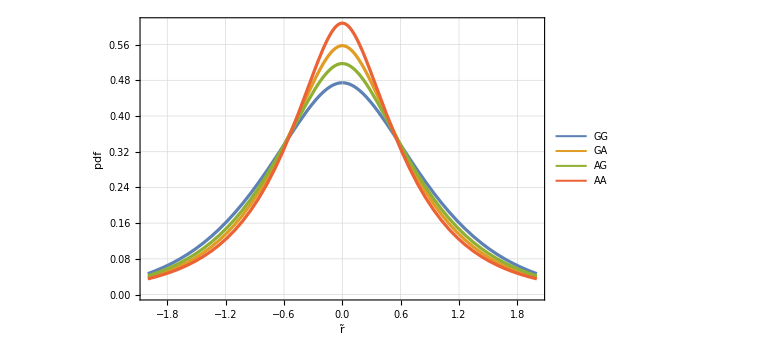

```mathematica
Plot[{PDFGaussianGaussian[R,5,1],PDFGaussianAlgebraic[R,100,55,5,1],PDFAlgebraicGaussian[R,100,55,5,1],PDFAlgebraicAlgebraic[R,100,55,55,5,1]},{R,-2,2}, FrameTicksStyle-> Directive[20],Frame->True, FrameStyle->Thickness[0.004], FrameLabel->{Style[OverTilde["r"],35],Style["pdf",35]}, PlotStyle->Thickness[0.004],ImageSize->Large,GridLines->Automatic, PlotLegends->{"GG","GA","AG","AA"}]
```

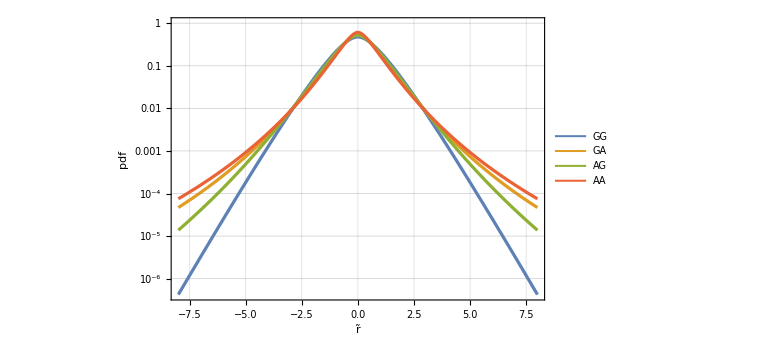

```mathematica
LogPlot[{PDFGaussianGaussian[R,5,1],PDFGaussianAlgebraic[R,100,55,5,1],PDFAlgebraicGaussian[R,100,55,5,1],PDFAlgebraicAlgebraic[R,100,55,55,5,1]},{R,-8,8}, FrameTicksStyle-> Directive[20],Frame->True, FrameStyle->Thickness[0.004], FrameLabel->{Style[OverTilde["r"],35],Style["pdf",35]}, PlotStyle->Thickness[0.004],ImageSize->Large,GridLines->Automatic, PlotLegends->{"GG","GA","AG","AA"}]
```